```mathematica
nestedTable[l_]:=Table[Append[l,y/@Range[2^(Length[l]-1)]],##]&@@Sequence[Table[{y[i],1,2^switch[l[[i]]]-1,2},{i,1,Length[l]}]]
```

```mathematica
fullIterate[l_]:=Table[nestedTable[x/@Range[Length[l]]],##]&@@Sequence[Table[{x[i],-1,l[[i]]},{i,1,Length[l]}]]
```

```mathematica
iterate[l_]:=Partition[fullIterate[l]//Flatten,2 Length[l]]
(*This seems to work better for large l*)
```

```mathematica
hierIterate[l_List,ki_List]:=Module[{k,i,hashEntry,hashMap},hashMap={};If[Length[l]==1,For[k=-1,k≤l[[1]],k++,For[i=1,i≤2^switch[k]-1,i+=2,hashEntry={Append[Append[ki,k+2],i]};
hashMap=Join[hashMap,hashEntry];]];Return[hashMap];
,
For[k=-1,k≤l[[1]],k++,
For[i=1,i≤2^switch[k]-1,i+=2,hashEntry=hierIterate[l[[2;;]],Append[Append[ki,k+2],i]];hashMap=Join[hashMap,hashEntry]]];Return[hashMap];
]]
(*This is working*)

hierIterate[l_List]:=hierIterate[l,{}]
(*This is working*)
(*This seems to work better for smaller norm l*)
```

```mathematica
iteratetimes=Table[Timing[iterate[{n,n}]][[1]],{n,1,10}]
iterate2times=Table[Timing[hierIterate[{n,n}]][[1]],{n,1,10}]
```

```mathematica
iteratetimes={0.00035,0.000556,0.001065,0.002563,0.008753,0.025627,0.084023,0.311622,1.253459,4.930502,19.5331}
```

{0.00035,0.000556,0.001065,0.002563,0.008753,0.025627,0.084023,0.311622,1.25346,4.9305,19.5331}

```mathematica
iterate2times={0.000232,0.000298,0.000733,0.001943,0.005841,0.022197,0.09121,0.495271,3.046761,20.115461,140.539}
```

{0.000232,0.000298,0.000733,0.001943,0.005841,0.022197,0.09121,0.495271,3.04676,20.1155,140.539}

```mathematica
iteratetimes3=Table[Timing[iterate[{n,n,n}]][[1]],{n,1,7}]
iterate2times3=Table[Timing[hierIterate[{n,n,n}]][[1]],{n,1,7}]
```

{0.001132,0.003294,0.013748,0.052433,0.300568,2.1505,16.1603}

{0.000576,0.001489,0.006037,0.035095,0.2066,1.66507,15.1651}

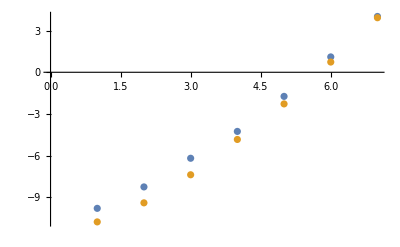

```mathematica
ListPlot[{iteratetimes3,iterate2times3}//Log2]
```

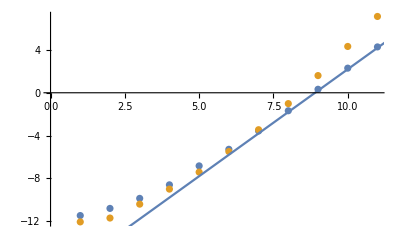

```mathematica
Show[ListPlot[{iteratetimes,iterate2times}//Log2],Plot[2x-17.8,{x,0,20}]]
```

```mathematica
Table[x,##]&@@Sequence[Table[{x[i],1,3},{i,1,2}]]
```

{{x,x,x},{x,x,x},{x,x,x}}